```mathematica
(*Capacitante function parameters*)
SetDirectory[NotebookDirectory[]];
α = 0.3; θ1=30;θ2=30;
(*Ct[t_]=Which[Mod[t,T]<α T,1,Mod[t,T]<α T+(1-C0)/(θ1 /T)1,1-(Mod[t,T]-α T)θ1/ T, Mod[t,T]<T-(1-C0)/(θ2 /T),C0, True,C0+(Mod[t,T]-T+(1-C0)/(θ2/ T))θ2/ T];
Ctd[t_]=Which[Mod[t,T]<α T,0,Mod[t,T]<α T+(1-C0)/(θ1/ T),-θ1/ T, Mod[t,T]<T-(1-C0)/(θ2/ T),0, True,θ2/ T];*)
```

```mathematica
ClearAll[V,M,H,NN,Va,Ma,NNa,t]
(*HH Parameters from doi:10.1371/journal.pone.0081402.t001, Give persistent oscillation*)
(*αm=0.1;
βm=4;
αh=0.07;
βh=1;
αn=0.01;
βn=0.125;
ENa=115;
EK=-12;
EL=10.6;
Voffset =-65;
Vrest=0;
mrest=0.05;
hrest=0.6;
nrest=0.3;
Vαm=25;
Vβm=0;
Vαh=0;
Vβh=30;
Vαn=10;
Vβn=0;
gNa=120;
gK=36;
gL=0.3;
Kαm=10;
Kβm=18;
Kαh=20;
Kβh=10;
Kαn=10;
Kβn=80;
Cm=1;*)
(*HH Parameters from https://www.st-andrews.ac.uk/~wjh/hh_model_intro/, Doesnt seem to be stimulated*)
αm=0.1;
βm=4;
αh=0.07;
βh=1;
αn=0.01;
βn=0.125;
ENa=115;
EK=-12;
EL=10.6;
Voffset =-65;
Vrest=0;
mrest=0.05;
hrest=0.596;
nrest=0.315;
Vαm=25;
Vβm=0;
Vαh=0;
Vβh=30;
Vαn=10;
Vβn=0;
gNa=120;
gK=36;
gL=0.3;
Kαm=10;
Kβm=18;
Kαh=20;
Kβh=10;
Kαn=10;
Kβn=80;
Cm=1;

(*freq parameter IC*)
w1=10;
η=2Pi *10/1000;
w2=w1+η;

(*firerate list*)
fRateHH={};
fRateHHs={};

(*Threshold*)
threshold=60;
(*Total time of simulation*)
maxtime=100;

(*Ionic Chanels*)
Am[V_]=αm (V-Vαm)/(1-Exp[-(V-Vαm)/Kαm]);
Bm[V_]=βm Exp[-(V-Vβm)/Kβm];
Ah[V_]=αh Exp[-(V-Vαh)/Kαh];
Bh[V_]=βh/(1+Exp[-(V-Vβh)/Kβh]);
An[V_]=αn (V-Vαn)/(1-Exp[-(V-Vαn)/Kαn]);
Bn[V_]=βn Exp[-(V-Vβn)/Kβn];

(*Solving HH*)
simulation={};
η=2Pi freq/1000;
maxtime=1000;(*In miliseconds*)
C0=0.75;T=30;
filename=StringJoin["HH_",ToString[T],"_C0_",ToString[T],"hz.csv"];
τ2=0.4;τ4=1;
```

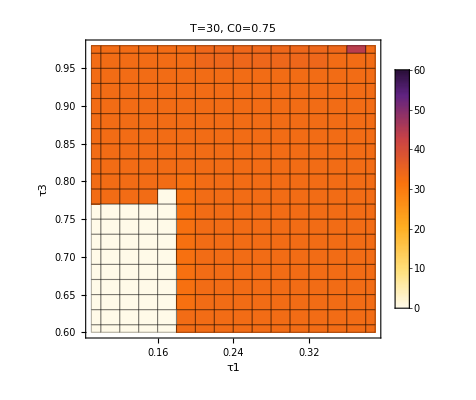

HH_30_C0_0.75.png

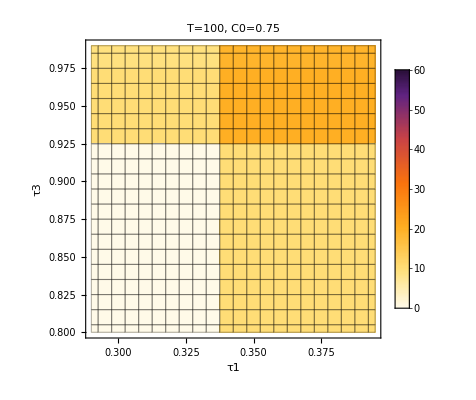

HH_100_C0_0.75.png

```mathematica
ClearAll[V,M,H,NN,Va,Ma,NNa,t]
(*HH Parameters from doi:10.1371/journal.pone.0081402.t001, Give persistent oscillation*)
(*αm=0.1;
βm=4;
αh=0.07;
βh=1;
αn=0.01;
βn=0.125;
ENa=115;
EK=-12;
EL=10.6;
Voffset =-65;
Vrest=0;
mrest=0.05;
hrest=0.6;
nrest=0.3;
Vαm=25;
Vβm=0;
Vαh=0;
Vβh=30;
Vαn=10;
Vβn=0;
gNa=120;
gK=36;
gL=0.3;
Kαm=10;
Kβm=18;
Kαh=20;
Kβh=10;
Kαn=10;
Kβn=80;
Cm=1;*)
(*HH Parameters from https://www.st-andrews.ac.uk/~wjh/hh_model_intro/, Doesnt seem to be stimulated*)
αm=0.1;
βm=4;
αh=0.07;
βh=1;
αn=0.01;
βn=0.125;
ENa=115;
EK=-12;
EL=10.6;
Voffset =-65;
Vrest=0;
mrest=0.05;
hrest=0.596;
nrest=0.315;
Vαm=25;
Vβm=0;
Vαh=0;
Vβh=30;
Vαn=10;
Vβn=0;
gNa=120;
gK=36;
gL=0.3;
Kαm=10;
Kβm=18;
Kαh=20;
Kβh=10;
Kαn=10;
Kβn=80;
Cm=1;

(*freq parameter IC*)
w1=10;
η=2Pi *10/1000;
w2=w1+η;

(*firerate list*)
fRateHH={};
fRateHHs={};

(*Threshold*)
threshold=60;
(*Total time of simulation*)
maxtime=100;

(*Ionic Chanels*)
Am[V_]=αm (V-Vαm)/(1-Exp[-(V-Vαm)/Kαm]);
Bm[V_]=βm Exp[-(V-Vβm)/Kβm];
Ah[V_]=αh Exp[-(V-Vαh)/Kαh];
Bh[V_]=βh/(1+Exp[-(V-Vβh)/Kβh]);
An[V_]=αn (V-Vαn)/(1-Exp[-(V-Vαn)/Kαn]);
Bn[V_]=βn Exp[-(V-Vβn)/Kβn];

(*Solving HH*)
simulation={};
η=2Pi freq/1000;
maxtime=1000;(*In miliseconds*)
C0=0.75;T=30;
filename=StringJoin["HH_",ToString[T],"_C0_",ToString[T],"hz.csv"];
τ2=0.4;τ4=1;
Do[Do[
Ct[t_]=Which[Mod[t,T]<τ1 T,1,Mod[t,T]<τ2 T,1+(C0-1)(Mod[t,T]-τ1 T)/((τ2-τ1)T), Mod[t,T]<τ3 T,C0, True,C0+(Mod[t,T] - τ3 T)(1-C0)/((τ4-τ3)T)];
Ctd[t_]=Which[Mod[t,T]<τ1 T,0,Mod[t,T]<τ2 T,(C0-1)/((τ2-τ1)T),Mod[t,T]< τ3 T,0, True,(1-C0)/((τ4-τ3)T)];
{V,M,H,NN}=NDSolveValue[{Ct[t] v'[t]==-Ctd[t] (v[t]+Voffset)-gNa m[t]^3 h[t](v[t]-ENa)-gK n[t]^4(v[t]-EK) -gL(v[t]-EL),
m'[t]==Am[v[t]](1-m[t])-Bm[v[t]]m[t],
h'[t]==Ah[v[t]](1-h[t])-Bh[v[t]] h[t],
n'[t]==An[v[t]](1-n[t])-Bn[v[t]]n[t],
v[0]==Vrest,m[0]==mrest,h[0]==hrest,n[0]==nrest},
{v,m,h,n},{t,0,maxtime}];
peaksHH = FindPeaks[Table[V[t],{t,0,maxtime,1}],0,0,threshold];
countHH=Length[peaksHH];
pointHH = {τ1,τ3,N[countHH/maxtime *1000]};
fRateHH = Append[fRateHH,pointHH];
(*Plot[Voffset+V[t],{t,0,maxtime},PlotRange->{-100,80}]*)
(*,{τ1,0.395,0.395,0.1}],{τ3,0.995,0.995,0.1}];*)
,{τ1,0.09,0.398,0.02}],{τ3,0.6,0.998,0.02}];
(*Plot[Ct[t],{t,0,maxtime},PlotRange->{0,1}]*)
(*Plot[Voffset+V[t],{t,0,maxtime},PlotRange->{-100,80}]
fRateHH*)
extract=fRateHH[[All,{1,2,3}]];
g1= ListDensityPlot[extract,Mesh->All,InterpolationOrder->0,PlotLegends->BarLegend[{Automatic,{0,60}}],PlotLegends->Automatic,PlotRange->{Full,Full,{0,60}},PlotRangeClipping->False,
ColorFunction->(ColorData["SunsetColors"][0.9(1-#/60)+0.07]&),ColorFunctionScaling->False,PlotLabel->StringJoin["T=",ToString[T],", C0=",ToString[C0]],FrameLabel->{"τ1","τ3"}]
filename=StringJoin["HH_",ToString[T],"_C0_",ToString[C0],".png"];
Export[filename,g1]
```

```mathematica
FrHH=fRateHH[[All,{1,2,3}]]; 
plot1=ListDensityPlot[FrHH,Mesh->All,InterpolationOrder->0,PlotRange->{Full,Full,Full},PlotRangeClipping->False,PlotLegends->Automatic,ColorFunction->(ColorData["SunsetColors"][(1-#)]&),ColorFunctionScaling->True, PlotLabel->"HH"];
FrHHs=fRateHHs[[All,{1,2,3}]]; 
plot2=ListDensityPlot[FrHHs,Mesh->All,InterpolationOrder->0,PlotRange->{Full,Full,Full},PlotRangeClipping->False,PlotLegends->Automatic,ColorFunction->(ColorData["SunsetColors"][(1-#)]&),ColorFunctionScaling->True, PlotLabel->"HH smoothed"];

GraphicsRow[{plot1 , plot2}, Spacings->0]

(*Export["dataFrHH.csv",FrHH]*)
```

-Graphics-

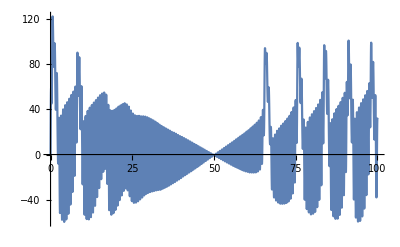

```mathematica
w1=10;
η=2Pi *10/1000;
w2=w1+η;
A=30;
B=30;
{V,M,H,NN}=NDSolveValue[{Cm v'[t]==(A*w1*Cos[w1*t]+B*w2*Cos[w2*t])-gNa m[t]^3 h[t](v[t]-ENa)-gK n[t]^4(v[t]-EK) -gL(v[t]-EL),
m'[t]==Am[v[t]](1-m[t])-Bm[v[t]]m[t],
h'[t]==Ah[v[t]](1-h[t])-Bh[v[t]] h[t],
n'[t]==An[v[t]](1-n[t])-Bn[v[t]]n[t],
v[0]==Vrest,m[0]==mrest,h[0]==hrest,n[0]==nrest},
{v,m,h,n},{t,0,maxtime}];
Plot[V[t],{t,0,maxtime}]
peaksHH = FindPeaks[Table[V[t],{t,0,maxtime,1}],0,0,threshold];
countHH=Length[peaksHH];
pointHH = {A,B,N[countHH/maxtime *1000]};
fRateHH = Append[fRateHH,pointHH];
```

0.995

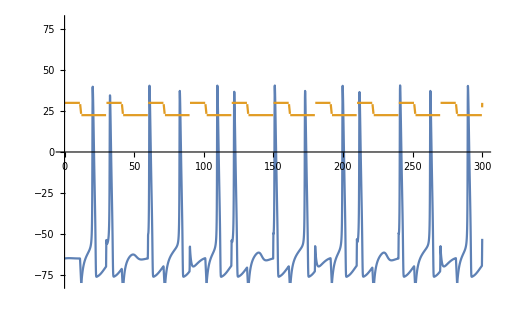

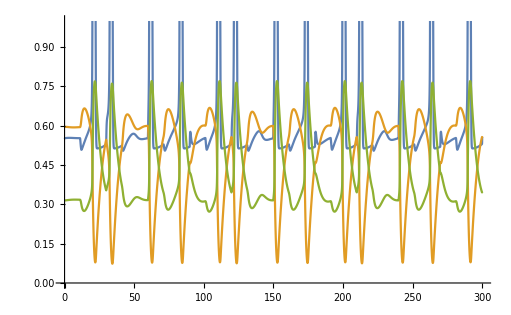

```mathematica
τ1=0.37;τ3=0.995
Ct[t_]=Which[Mod[t,T]<τ1 T,1,Mod[t,T]<τ2 T,1+(C0-1)(Mod[t,T]-τ1 T)/((τ2-τ1)T), Mod[t,T]<τ3 T,C0, True,C0+(Mod[t,T] - τ3 T)(1-C0)/((τ4-τ3)T)];
Ctd[t_]=Which[Mod[t,T]<τ1 T,0,Mod[t,T]<τ2 T,(C0-1)/((τ2-τ1)T),Mod[t,T]< τ3 T,0, True,(1-C0)/((τ4-τ3)T)];
{V,M,H,NN}=NDSolveValue[{Ct[t] v'[t]==-Ctd[t] (v[t]+Voffset)-gNa m[t]^3 h[t](v[t]-ENa)-gK n[t]^4(v[t]-EK) -gL(v[t]-EL),
m'[t]==Am[v[t]](1-m[t])-Bm[v[t]]m[t],
h'[t]==Ah[v[t]](1-h[t])-Bh[v[t]] h[t],
n'[t]==An[v[t]](1-n[t])-Bn[v[t]]n[t],
v[0]==Vrest,m[0]==mrest,h[0]==hrest,n[0]==nrest},
{v,m,h,n},{t,0,maxtime}];

Plot[{Voffset+V[t],30*Ct[t]},{t,0,300},PlotRange->{-80,80}]
Plot[{0.5+M[t],H[t],NN[t]},{t,0,300},PlotRange->{0,1}]
```